```mathematica
ClearAll["Global`*"];
τ0=2.6×10^-8; 
c=3×10^8;
```

```mathematica
τ= (τ0)/√(1-(v^2)/(c^2))
```

(2.6×10^-8)/(√(1-v^2/90000000000000000))

```mathematica
zk[v_]=τ0 *v
```

2.6×10^-8 v

```mathematica
zr[v_] = τ *v
```

(2.6×10^-8 v)/(√(1-v^2/90000000000000000))

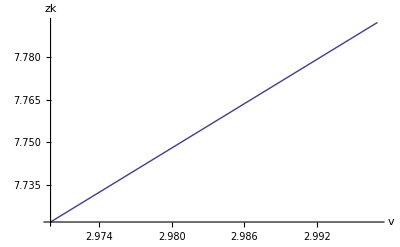

```mathematica
Plot[zk[v*(10^8)], {v,0.990*c*10^(-8),0.999*c*10^-8},
AxesLabel -> {"v", "zk"}]
```